# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

```mathematica
modePR=<|
"params_deep"->"params",
"params_shallow"->"params",
"rxns_deep"->"rxns",
"rxns_shallow"->"rxns"
|>;
```

```mathematica
tdirs=<|
"params"->"../training_data/training_data_params/",
"rxns"->"../training_data/training_data_rxns/"
|>;

freqs=Association[];

SetDirectory[NotebookDirectory[]];
Do[
tdir=tdirs[td];
freqs[td]=Flatten[Import[tdir<>"freqs.txt","Table"]];
,{td,Keys[tdirs]}];
```

```mathematica
noTpts=400;
```

# Analytic time evolution of moment

```mathematica
getNvar[mu_,cov_]:=cov+KroneckerProduct[mu,mu];
```

```mathematica
getN3[mu_,nvar_,i_,j_,k_]:=-2*mu[[i]]*mu[[j]]*mu[[k]]+mu[[i]]*nvar[[j,k]]+mu[[j]]*nvar[[i,k]]+mu[[k]]*nvar[[i,j]]
```

```mathematica
getN4[mu_,nvar_,i_,j_,k_,l_]:=-2*mu[[i]]*mu[[j]]*mu[[k]]*mu[[l]]+nvar[[i,j]]*nvar[[k,l]]+nvar[[i,k]]*nvar[[j,l]]+nvar[[i,l]]*nvar[[j,k]]
```

```mathematica
getAnalytic[moment_]:=Module[
{b,w,muh,mu,varh,cov,prec,repIxnsFromTime,repIxnsToTime,repF,nVec,pt,derivPt,analytic,n1Reps,nvar,n2Reps,n3Reps,n4Reps,analyticEval}
,
b={b1,b2};
w={{w11},{w12}};
muh={muh1};
mu=Join[b+w.muh,muh];

varh={{varh11}};
cov=ArrayFlatten[{{w.Transpose[w]+sig2*IdentityMatrix[2],w.varh},{varh.Transpose[w],varh}}];
prec=Inverse[cov];

repIxnsToTime={b1->b1[t],b2->b2[t],muh1->muh1[t],w11->w11[t],w12->w12[t],sig2->sig2[t],varh11->varh11[t]};
repIxnsFromTime={b1[t]->b1,b2[t]->b2,muh1[t]->muh1,w11[t]->w11,w12[t]->w12,sig2[t]->sig2,varh11[t]->varh11};
repF={b1'[t]->fb1,b2'[t]->fb2,muh1'[t]->fmuh1,w11'[t]->fw11,w12'[t]->fw12,sig2'[t]->fsig2,varh11'[t]->fvarh11};

nVec={n1,n2,n3};

pt=Exp[(-1/2)*Transpose[nVec-mu].prec.(nVec-mu)]/Sqrt[(2Pi)^3*Det[cov]];
derivPt=Simplify[(D[pt/.repIxnsToTime,t]/.repIxnsFromTime/.repF)/pt];

analytic=moment*derivPt;

(* Substitute n *)
nvar=getNvar[mu,cov];

n1Reps=Simplify[DeleteDuplicates[Flatten[Table[ToExpression["n"<>ToString[i]]->mu[[i]],{i,1,3}]]]];

n2Reps=Simplify[DeleteDuplicates[Flatten[Table[ToExpression["n"<>ToString[i]]*ToExpression["n"<>ToString[j]]->nvar[[i,j]],{i,1,3},{j,1,3}]]]];

n3Reps=Simplify[DeleteDuplicates[Flatten[Table[ToExpression["n"<>ToString[i]]*ToExpression["n"<>ToString[j]]*ToExpression["n"<>ToString[k]]->getN3[mu,nvar,i,j,k],{i,1,3},{j,1,3},{k,1,3}]]]];

n4Reps=Simplify[DeleteDuplicates[Flatten[Table[ToExpression["n"<>ToString[i]]*ToExpression["n"<>ToString[j]]*ToExpression["n"<>ToString[k]]*ToExpression["n"<>ToString[l]]->getN4[mu,nvar,i,j,k,l],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]]]];

analyticEval=Simplify[Expand[analytic]/.n4Reps/.n3Reps/.n2Reps/.n1Reps];

Return[analyticEval]
]
```

```mathematica
analytic=getAnalytic[n1*n3]
```

b1 fmuh1+fb1 muh1+fw11 muh1^2+fw11 varh11+fvarh11 w11+2 fmuh1 muh1 w11

# Real parameters

## Setup

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir="../../"<>getCacheDirRaw[volExp,noIP3R];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{2118.58,6323.61},{1934.71,5726.05}}

## Data

```mathematica
SetDirectory[NotebookDirectory[]];

ip3s={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

filtered0=Association[];
derivs0=Association[];
Monitor[
Do[
ip3=ip3s[[idx]];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"filtered0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

filtered0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"derivs0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

derivs0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]]
```

# Import params

## Fourier

```mathematica
fourier[offset_,sinCoeffs_,cosCoeffs_,freqs_,tptPlt_]:=Module[
{range,pts}
,
range=Max[Total[Abs[sinCoeffs]+Abs[cosCoeffs]]+10^-8,1];
pts=Table[offset[[1]]+(Sum[sinCoeffs[[i]]*Sin[freqs[[i]]*(tpt-1)]+cosCoeffs[[i]]*Cos[freqs[[i]]*(tpt-1)],{i,Length[freqs]}])/range,{tpt,tptPlt}];

Return[pts];
];
```

```mathematica
fourierMuh=Association[];
fourierVarh=Association[];
muhSinCoeffSt=Association[];
muhCosCoeffSt=Association[];
varhSinCoeffSt=Association[];
varhCosCoeffSt=Association[];

Do[

fourierMuh[mode]=Association[];
fourierVarh[mode]=Association[];
muhSinCoeffSt[mode]=Association[];
muhCosCoeffSt[mode]=Association[];
varhSinCoeffSt[mode]=Association[];
varhCosCoeffSt[mode]=Association[];

Do[
(* Import *)
SetDirectory[NotebookDirectory[]];
trained=Import["trained/"<>mode<>"/"<>IntegerString[iRun,10,2]<>".wlnet"];

(* Extract coeffs *)
arrs=Information[trained,"Arrays"];
muhOffset=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","offset","Array"}]];
muhCosCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","cosCoeff","Array"}]];
muhSinCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","sinCoeff","Array"}]];
If[muhCosCoeff[[1]]<0,
muhCosCoeff*=-1;
muhSinCoeff*=-1;
];

muhSinCoeffSt[mode][iRun]=muhSinCoeff;
muhCosCoeffSt[mode][iRun]=muhCosCoeff;

varhOffset=Normal[arrs[{"inputsWOSTD","convert0","layerVarh","offset","Array"}]];
varhCosCoeff=
Normal[arrs[{"inputsWOSTD","convert0","layerVarh","cosCoeff","Array"}]];
varhSinCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerVarh","sinCoeff","Array"}]];
If[varhCosCoeff[[1]]<0,
varhCosCoeff*=-1;
varhSinCoeff*=-1;
];

varhSinCoeffSt[mode][iRun]=varhSinCoeff;
varhCosCoeffSt[mode][iRun]=varhCosCoeff;

(* Plot *)
tptsPlt=Table[tpt,{tpt,1,noTpts}];
fourierMuh[mode][iRun]=fourier[muhOffset,muhSinCoeff,muhCosCoeff,freqs[modePR[mode]],tptsPlt];
fourierVarh[mode][iRun]=fourier[varhOffset,varhSinCoeff,varhCosCoeff,freqs[modePR[mode]],tptsPlt];
,{iRun,1,10}];
,{mode,{"params_deep","rxns_deep","params_shallow","rxns_shallow"}}];
```

## Import params

```mathematica
(* Import *)
SetDirectory[NotebookDirectory[]];
paramsIntegratedLD=Association[];
Do[
paramsIntegratedLD[mode]=Association[];
Do[
paramsIntegratedLD[mode][iNet]=Association[];
params=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx"];

Do[
paramsLD=params[ip3]["LD"];
paramsIntegratedLD[mode][iNet][ip3]=Table[
convertParamsLatentSpace[paramsLD[[tpt]],{fourierMuh[mode][iNet][[tpt]]},{{fourierVarh[mode][iNet][[tpt]]}}]
,{tpt,1,Length[paramsLD]-2}];
,{ip3,Keys[params]}];
,{iNet,1,10}];
,{mode,{"params_deep","params_shallow","rxns_deep","rxns_shallow"}}];
```

# Plot integrated params

```mathematica
ip3="ip3_0p700";
ip3Label="[IP3]=0.7μM";

muTrue=Association[];
n2True=Association[];
Do[
muTrue[mode]=Association[];
n2True[mode]=Association[];

Do[
muTrue[mode][iNet]={};
n2True[mode][iNet]={};

Do[
params=paramsIntegratedLD[mode][iNet][ip3][[tpt]];
moments=convertParamsToMoments[nv,params];
AppendTo[muTrue[mode][iNet],moments["mu"][[1]]];
AppendTo[n2True[mode][iNet],moments["var"][[1,1]]+(moments["mu"][[1]])^2];

,{tpt,1,399}];
,{iNet,1,10}];
,{mode,{"rxns_shallow","params_shallow","rxns_deep","params_deep"}}];

muSS={};
n2SS={};
Do[
paramsSS=filtered0[ip3]["LD"][[tpt]];
momentsSS=convertParamsToMoments[nv,paramsSS];
AppendTo[muSS,momentsSS["mu"][[1]]];
AppendTo[n2SS,momentsSS["var"][[1,1]]+(momentsSS["mu"][[1]])^2];
 ,{tpt,1,399}];
```

```mathematica
getMeanWithError[vals_]:=Module[
{mean,std,around}
,
mean=Mean[Values[vals]];
std=StandardDeviation[Values[vals]];
around=Table[Around[mean[[i]],std[[i]]],{i,Length[mean]}];
Return[around]
];
```

```mathematica
getMeanWithoutError[vals_]:=Mean[Values[vals]];
```

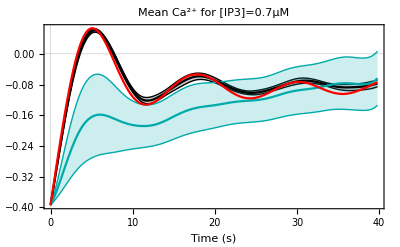
-Graphics- |

```mathematica
times=Table[0.1*(t-1),{t,1,Length[muTrue["rxns_shallow"][1]]}];
leg=LineLegend[{Black,Darker[Cyan],Red},{"DBD (rxns)","DBD (params)","Stoch. Sims."}];
p=ListLinePlot[{
Transpose[{times,getMeanWithError[muTrue["rxns_shallow"]]}],
Transpose[{times,getMeanWithError[muTrue["params_shallow"]]}],
Transpose[{times,muSS}]
},PlotRange->All,PlotLabel->"Mean Ca^(2+) for "<>ip3Label,PlotStyle->{Black,Darker[Cyan],Red},FrameLabel->{"Time (s)"},IntervalMarkers->"Bands"];
Grid[{{p,leg}}]
```

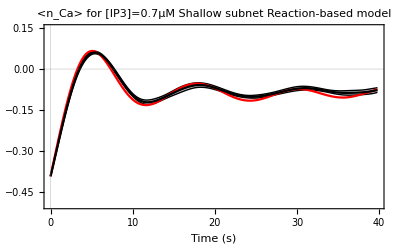
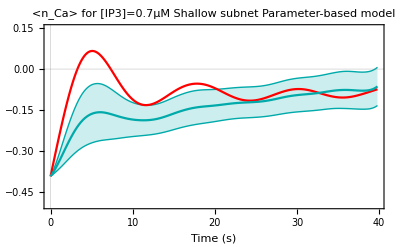
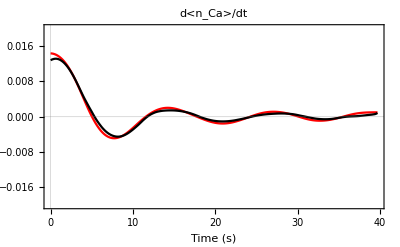
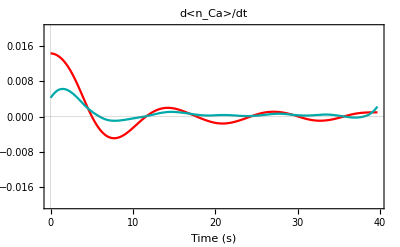
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

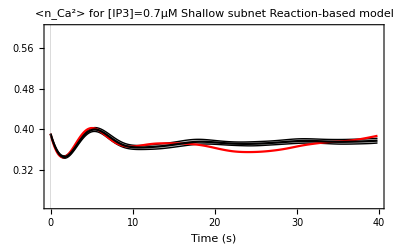
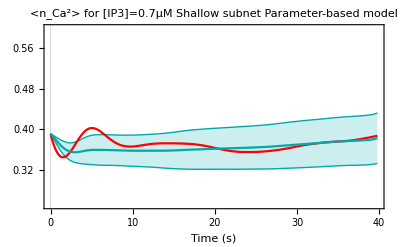
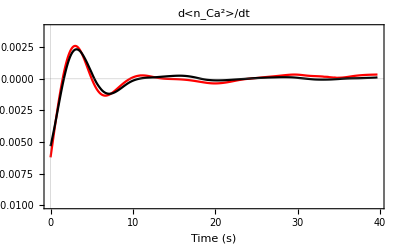
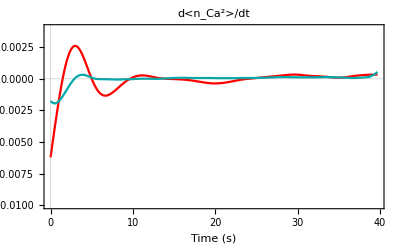
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
colors=<|
"rxns_deep"->Black,
"rxns_shallow"->Black,
"params_deep"->Darker[Cyan],
"params_shallow"->Darker[Cyan]
|>;

labels=<|
"rxns_deep"->"\nDeep subnet\nReaction-based model",
"rxns_shallow"->"\nShallow subnet\nReaction-based model",
"params_deep"->"\nDeep subnet\nParameter-based model",
"params_shallow"->"\nShallow subnet\nParameter-based model"
|>;

pTrue=Association[];
pTrue["mu"]=Association[];
pTrue["muDeriv"]=Association[];
pTrue["n2"]=Association[];
pTrue["n2Deriv"]=Association[];
Do[
muVals=getMeanWithError[muTrue[mode]];
n2Vals=getMeanWithError[n2True[mode]];
muValsWE=getMeanWithoutError[muTrue[mode]];
n2ValsWE=getMeanWithoutError[n2True[mode]];

pTrue["mu"][mode]=ListLinePlot[{
Transpose[{times,muSS}],
Transpose[{times,muVals}]
},PlotLabel->"<n_Ca> for "<>ip3Label<>labels[mode],PlotStyle->{Red,colors[mode]},FrameLabel->{"Time (s)"},PlotRange->{-0.5,0.15},IntervalMarkers->"Bands"];

pTrue["muDeriv"][mode]=ListLinePlot[{
Transpose[{times[[;;-2]],muSS[[2;;]]-muSS[[;;-2]]}],
Transpose[{times[[;;-2]],muValsWE[[2;;]]-muValsWE[[;;-2]]}]
},PlotLabel->"d<n_Ca>/dt",PlotStyle->{Red,colors[mode]},FrameLabel->{"Time (s)"},PlotRange->{-0.02,0.02},IntervalMarkers->"Bands"];

pTrue["n2"][mode]=ListLinePlot[{
Transpose[{times,n2SS}],
Transpose[{times,n2Vals}]
},PlotLabel->"<n_Ca^2> for "<>ip3Label<>labels[mode],PlotStyle->{Red,colors[mode]},FrameLabel->{"Time (s)"},PlotRange->{0.25,0.6},IntervalMarkers->"Bands"];

pTrue["n2Deriv"][mode]=ListLinePlot[{
Transpose[{times[[;;-2]],n2SS[[2;;]]-n2SS[[;;-2]]}],
Transpose[{times[[;;-2]],n2ValsWE[[2;;]]-n2ValsWE[[;;-2]]}]
},PlotLabel->"d<n_Ca^2>/dt",PlotStyle->{Red,colors[mode]},FrameLabel->{"Time (s)"},PlotRange->{-0.01,0.004},IntervalMarkers->"Bands"];
,{mode,{"rxns_shallow","rxns_deep","params_shallow","params_deep"}}];

leg=LineLegend[{Black,Darker[Cyan],Red},{"DBD (rxns)","DBD (params)","Stoch. Sims."}];

Grid[{{
pTrue["mu"]["rxns_shallow"],pTrue["mu"]["params_shallow"],leg
},{
pTrue["muDeriv"]["rxns_shallow"],pTrue["muDeriv"]["params_shallow"],leg
}}]

Grid[{{
pTrue["n2"]["rxns_shallow"],pTrue["n2"]["params_shallow"],leg
},{
pTrue["n2Deriv"]["rxns_shallow"],pTrue["n2Deriv"]["params_shallow"],leg
}}]
```

# Substitute

```mathematica
getDerivs[params_,paramsNext_]:=<|
"wt"->paramsNext["wt"]-params["wt"],
"b"->paramsNext["b"]-params["b"],
"sig2"->paramsNext["sig2"]-params["sig2"],
"muh"->paramsNext["muh"]-params["muh"],
"varh"->paramsNext["varh"]-params["varh"]
|>;
```

```mathematica
evaluateFull[analyticEval_,params_,paramsNext_]:=Module[
{subSubs,analyticSub,derivs,repDerivs}
,
subSubs={
sig2->params["sig2"],
muh1->params["muh"][[1]],
varh11->params["varh"][[1,1]],
w11->params["wt"][[1,1]],
w12->params["wt"][[1,2]],
b1->params["b"][[1]],
b2->params["b"][[2]]
};

analyticSub=Simplify[analyticEval/.subSubs];

derivs=getDerivs[params,paramsNext];
repDerivs={
fsig2->derivs["sig2"],
fmuh1->derivs["muh"][[1]],
fvarh11->derivs["varh"][[1,1]],
fw11->derivs["wt"][[1,1]],
fw12->derivs["wt"][[1,2]],
fb1->derivs["b"][[1]],
fb2->derivs["b"][[2]]
};

Return[analyticSub/.repDerivs]
]
```

```mathematica
evaluateTerms[analyticEval_,params_,paramsNext_]:=Module[
{subSubs,analyticSub,terms,derivs,repDerivs}
,
subSubs={
sig2->params["sig2"],
muh1->params["muh"][[1]],
varh11->params["varh"][[1,1]],
w11->params["wt"][[1,1]],
w12->params["wt"][[1,2]],
b1->params["b"][[1]],
b2->params["b"][[2]]
};

analyticSub=Simplify[analyticEval/.subSubs];

derivs=getDerivs[params,paramsNext];
repDerivs={
fsig2->derivs["sig2"],
fmuh1->derivs["muh"][[1]],
fvarh11->derivs["varh"][[1,1]],
fw11->derivs["wt"][[1,1]],
fw12->derivs["wt"][[1,2]],
fb1->derivs["b"][[1]],
fb2->derivs["b"][[2]]
};

terms=<|
"fsig2"->(Coefficient[analyticSub,fsig2]*fsig2/.repDerivs),
"fmuh1"->(Coefficient[analyticSub,fmuh1]*fmuh1/.repDerivs),
"fvarh11"->(Coefficient[analyticSub,fvarh11]*fvarh11/.repDerivs),
"fw11"->(Coefficient[analyticSub,fw11]*fw11/.repDerivs),
"fw12"->(Coefficient[analyticSub,fw12]*fw12/.repDerivs),
"fb1"->(Coefficient[analyticSub,fb1]*fb1/.repDerivs),
"fb2"->(Coefficient[analyticSub,fb2]*fb2/.repDerivs)
|>;

Return[terms]
]
```

```mathematica
evaluateTermsWithoutF[analyticEval_,params_]:=Module[
{subSubs,analyticSub,terms}
,
subSubs={
sig2->params["sig2"],
muh1->params["muh"][[1]],
varh11->params["varh"][[1,1]],
w11->params["wt"][[1,1]],
w12->params["wt"][[1,2]],
b1->params["b"][[1]],
b2->params["b"][[2]]
};

analyticSub=Simplify[analyticEval/.subSubs];

terms=<|
"fsig2"->Coefficient[analyticSub,fsig2],
"fmuh1"->Coefficient[analyticSub,fmuh1],
"fvarh11"->Coefficient[analyticSub,fvarh11],
"fw11"->Coefficient[analyticSub,fw11],
"fw12"->Coefficient[analyticSub,fw12],
"fb1"->Coefficient[analyticSub,fb1],
"fb2"->Coefficient[analyticSub,fb2]
|>;

Return[terms]
]
```

## N1 (full to validate)

```mathematica
analytic=getAnalytic[n1];
```

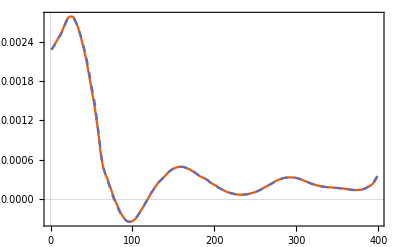

```mathematica
mode="rxns_deep";
iNet=1;
ip3="ip3_0p400";

derivsEval={};
derivsTrue={};
Do[
params=paramsIntegratedLD[mode][iNet][ip3][[tpt]];
paramsNext=paramsIntegratedLD[mode][iNet][ip3][[tpt+1]];
AppendTo[derivsEval,evaluateFull[analytic,params,paramsNext]];

muTrue=convertParamsToMoments[2,params]["mu"];
muNextTrue=convertParamsToMoments[2,paramsNext]["mu"];
AppendTo[derivsTrue,muNextTrue[[1]]-muTrue[[1]]];
,{tpt,1,399}];
ListLinePlot[{derivsEval,derivsTrue},PlotRange->All,PlotStyle->{Automatic,Dashed}]
```

## N1*N3 (full to validate)

```mathematica
analytic=getAnalytic[n1*n3];
```

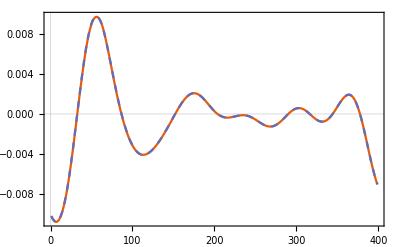

```mathematica
mode="rxns_deep";
iNet=1;
ip3="ip3_0p400";

derivsEval={};
derivsTrue={};
Do[
params=paramsIntegratedLD[mode][iNet][ip3][[tpt]];
paramsNext=paramsIntegratedLD[mode][iNet][ip3][[tpt+1]];
AppendTo[derivsEval,evaluateFull[analytic,params,paramsNext]];

muTrue=convertParamsToMoments[2,params]["mu"];
varTrue=convertParamsToMoments[2,params]["var"];
muNextTrue=convertParamsToMoments[2,paramsNext]["mu"];
varNextTrue=convertParamsToMoments[2,paramsNext]["var"];
n13=varTrue[[1,3]]+muTrue[[1]]*muTrue[[3]];
n13Next=varNextTrue[[1,3]]+muNextTrue[[1]]*muNextTrue[[3]];
AppendTo[derivsTrue,n13Next-n13];
,{tpt,1,399}];
ListLinePlot[{derivsEval,derivsTrue},PlotRange->All,PlotStyle->{Automatic,Dashed}]
```

## Plot methods

```mathematica
plt[terms_,color_,withError_]:=Module[
{mean,std,vals,times}
,
mean=Mean[Values[terms]];
If[withError,
std=StandardDeviation[Values[terms]];
vals=Table[Around[mean[[i]],std[[i]]],{i,Length[mean]}];
,
vals=mean;
];

times=Table[0.1*(t-1),{t,1,Length[vals]}];

Return[ListLinePlot[Transpose[{times,vals}],PlotStyle->color,IntervalMarkers->"Bands",PlotRange->All]];
]
```

```mathematica
pltSum[terms_,color_]:=Module[
{mean,vals,times}
,
vals=Table[getINet[terms,iNet],{iNet,1,10}];
mean=Mean[vals];
vals=Total[mean];
times=Table[0.1*(t-1),{t,1,Length[vals]}];
Return[ListLinePlot[Transpose[{times,vals}],PlotStyle->color,IntervalMarkers->"Bands",PlotRange->All]]
]
```

```mathematica
pltMany[terms_,fs_,colorb_,withError_,label_]:=Show[
Join[
Table[
plt[terms[f[[1]]],f[[2]],withError]
,{f,fs}],
{pltSum[terms,colorb]}
],
PlotRange->{-0.02,0.02},
FrameLabel->{"Time (s)"},
PlotLabel->label
]
```

## N1 by terms

```mathematica
analytic=getAnalytic[n1]
```

fb1+fw11 muh1+fmuh1 w11

```mathematica
ip3="ip3_0p700";
terms=Association[];

Do[
Print[mode];
terms[mode]=<|
"fsig2"->Association[],
"fmuh1"->Association[],
"fvarh11"->Association[],
"fw11"->Association[],
"fw12"->Association[],
"fb1"->Association[],
"fb2"->Association[]
|>;

Do[
Do[
terms[mode][k][iNet]={};
,{k,Keys[terms[mode]]}];

Do[
params=paramsIntegratedLD[mode][iNet][ip3][[tpt]];
paramsNext=paramsIntegratedLD[mode][iNet][ip3][[tpt+1]];
terms0=evaluateTerms[analytic,params,paramsNext];
(*terms0=evaluateTermsWithoutF[analytic,params];*)

Do[
AppendTo[terms[mode][k][iNet],terms0[k]];
,{k,Keys[terms0]}];
,{tpt,1,399}];
,{iNet,1,10}];
,{mode,{"rxns_shallow","params_shallow","rxns_deep","params_deep"}}];
```

rxns_shallow

params_shallow

rxns_deep

params_deep

## Plot

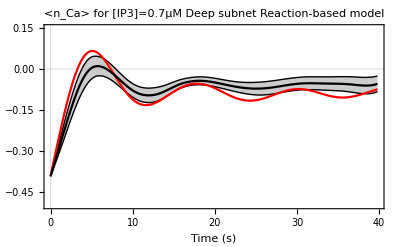
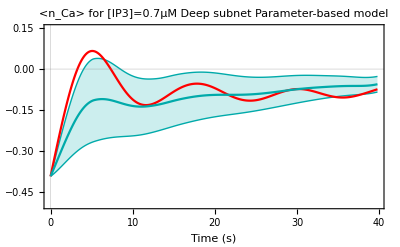
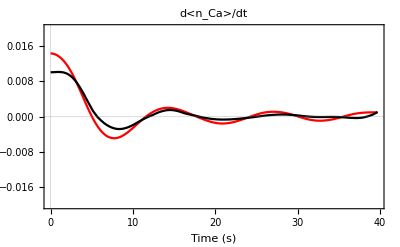
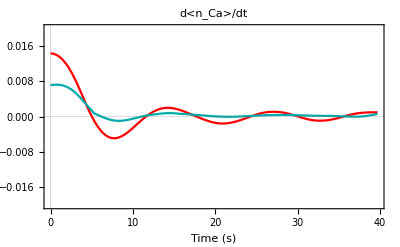
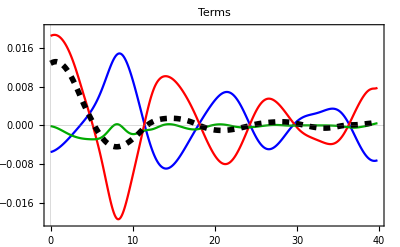
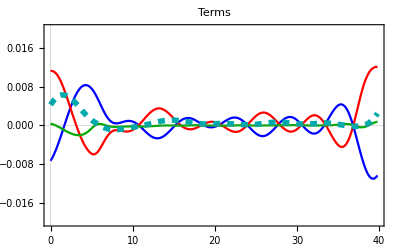
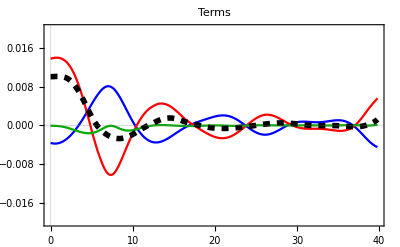
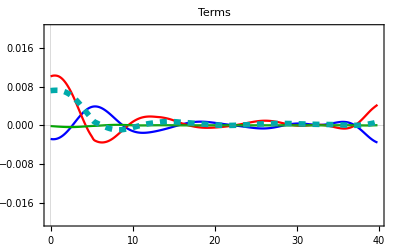
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
fcolors={{"fmuh1",Blue},{"fb1",Red},{"fw11",Darker[Green]}};
colorb1=Directive[Dashed,Black,Thickness[0.01]];
colorb2=Directive[Dashed,Darker[Cyan],Thickness[0.01]];

labels=<|
"fmuh1"->"(... x F_μ_h) term",
"fb1"->"(... x F_b_Ca) term",
"fw11"->"(... x F_W_(Ca, Ca)) term",
"fvarh11"->"(... x F_Σ_h) term"
|>;
leg=LineLegend[Join[fcolors[[;;,2]],{colorb1,colorb2}],Join[Table[labels[f[[1]]],{f,fcolors}],{"d<n_Ca>/dt = sum\nof all terms (rxns)","d<n_Ca>/dt = sum\nof all terms (params)"}]];
leg2=LineLegend[{Black,Darker[Cyan],Red},{"DBD (rxns)","DBD (params)","Stoch. Sims."}];

subnet="deep";
p=Grid[{{
pTrue["mu"]["rxns_shallow"],
pTrue["mu"]["params_shallow"],
pTrue["mu"]["rxns_deep"],
pTrue["mu"]["params_deep"],
leg2
},{
pTrue["muDeriv"]["rxns_shallow"],
pTrue["muDeriv"]["params_shallow"],
pTrue["muDeriv"]["rxns_deep"],
pTrue["muDeriv"]["params_deep"],
leg2
},{
pltMany[terms["rxns_shallow"],fcolors,colorb1,False,"Terms"],
pltMany[terms["params_shallow"],fcolors,colorb2,False,"Terms"],
pltMany[terms["rxns_deep"],fcolors,colorb1,False,"Terms"],
pltMany[terms["params_deep"],fcolors,colorb2,False,"Terms"],
leg
},{
pltMany[terms["rxns_shallow"],fcolors,colorb1,True,"Terms (with error bars)"],
pltMany[terms["params_shallow"],fcolors,colorb2,True,"Terms (with error bars)"],
pltMany[terms["rxns_deep"],fcolors,colorb2,True,"Terms (with error bars)"],
pltMany[terms["params_deep"],fcolors,colorb2,True,"Terms (with error bars)"]
}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures_moment_closure/terms_mu.pdf",p]
```

figures_moment_closure/terms_mu.pdf

## Plot integrated

```mathematica
pltAccumulated[muTrue_,terms_,fcolors_,colorb_,label_]:=Module[
{pAcc,muMeanTrue,times,p,fMean,fAcc}
,
muMeanTrue=Mean[Values[muTrue]];
pAcc={};
Do[
fMean=Mean[Values[terms[f[[1]]]]];

fAcc=muMeanTrue[[1]]+Join[{0},Accumulate[fMean]];
times=Table[0.1*(i-1),{i,Length[fAcc]}];

p=ListLinePlot[Transpose[{times,fAcc}],PlotStyle->f[[2]],PlotRange->All];
AppendTo[pAcc,p];
,{f,fcolors}];

p=Show[
pAcc,
ListLinePlot[Transpose[{times[[;;-2]],muMeanTrue}],PlotStyle->colorb,PlotRange->All],
PlotRange->{-0.75,0.25},
FrameLabel->{"Time (s)"},
PlotLabel->"<n_Ca> and integrated terms\n"<>label
];
Return[p]
]
```

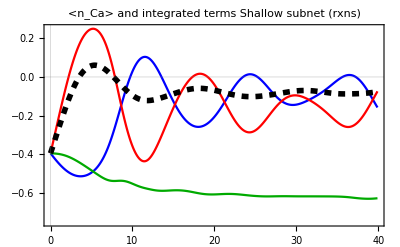
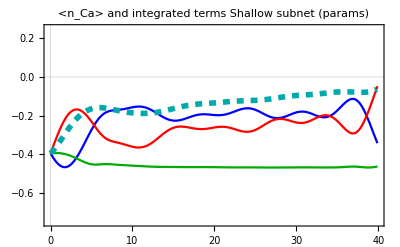
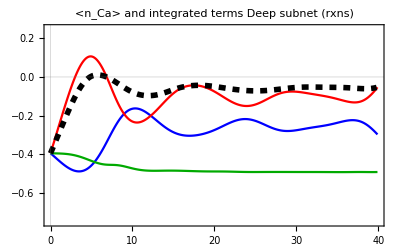
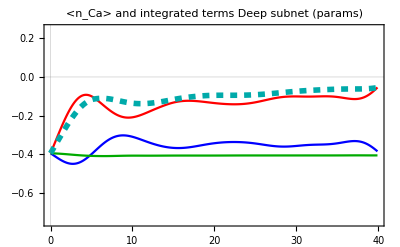
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
leg=LineLegend[Join[fcolors[[;;,2]],{colorb1,colorb2}],Join[Table[labels[f[[1]]],{f,fcolors}],{"<n_Ca> = sum\nof all terms (rxns)","<n_Ca> = sum\nof all terms (params)"}]];
p=Grid[{{
pltAccumulated[muTrue["rxns_shallow"],terms["rxns_shallow"],fcolors,colorb1,"Shallow subnet (rxns)"],
pltAccumulated[muTrue["params_shallow"],terms["params_shallow"],fcolors,colorb2,"Shallow subnet (params)"],
pltAccumulated[muTrue["rxns_deep"],terms["rxns_deep"],fcolors,colorb1,"Deep subnet (rxns)"],
pltAccumulated[muTrue["params_deep"],terms["params_deep"],fcolors,colorb2,"Deep subnet (params)"],
leg
}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures_moment_closure/terms_mu_int.pdf",p]
```

figures_moment_closure/terms_mu_int.pdf

## Plot Single net

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;Length[Values[terms][[1]]]]],Keys[Values[terms][[1]]]];
```

```mathematica
getINet[terms_,iNet_]:=Module[
{res}
,
res=Association[];
Do[
res[k]=terms[k][iNet];
,{k,Keys[terms]}];
Return[res];
];
```

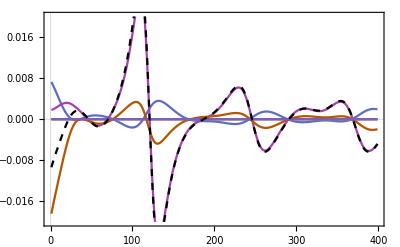
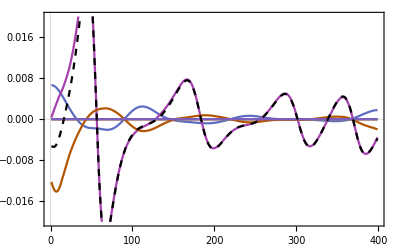
-Graphics- | -Graphics- |

```mathematica
iNet=1;
rng={-0.02,0.02};
Grid[{{
Show[
ListLinePlot[Values[getINet[terms["rxns_shallow"],iNet]],PlotRange->rng],
ListLinePlot[Total[Values[getINet[terms["rxns_shallow"],iNet]]],PlotRange->rng,PlotStyle->Directive[Black,Dashed]]
],
Show[
ListLinePlot[Values[getINet[terms["params_shallow"],iNet]],PlotRange->rng],
ListLinePlot[Total[Values[getINet[terms["params_shallow"],iNet]]],PlotRange->rng,PlotStyle->Directive[Black,Dashed]]
],
leg
}}]
```

## N1, terms, many ip3

## Many IP3

```mathematica
terms=Association[];

Do[
Print[ip3];
terms[ip3]=Association[];
Do[
terms[ip3][mode]=<|
"fsig2"->Association[],
"fmuh1"->Association[],
"fvarh11"->Association[],
"fw11"->Association[],
"fw12"->Association[],
"fb1"->Association[],
"fb2"->Association[]
|>;

Do[
Do[
terms[ip3][mode][k][iNet]={};
,{k,Keys[terms[ip3][mode]]}];

Do[
params=paramsIntegratedLD[mode][iNet][ip3][[tpt]];
paramsNext=paramsIntegratedLD[mode][iNet][ip3][[tpt+1]];
terms0=evaluateTerms[analytic,params,paramsNext];
(*terms0=evaluateTermsWithoutF[analytic,params];*)

Do[
AppendTo[terms[ip3][mode][k][iNet],terms0[k]];
,{k,Keys[terms0]}];
,{tpt,1,399}];
,{iNet,1,10}];
,{mode,{"rxns_shallow","params_shallow","rxns_deep","params_deep"}}];
,{ip3,{"ip3_0p200","ip3_0p400","ip3_0p600","ip3_0p800","ip3_1p000"}}];
```

ip3_0p200

ip3_0p400

ip3_0p600

ip3_0p800

ip3_1p000

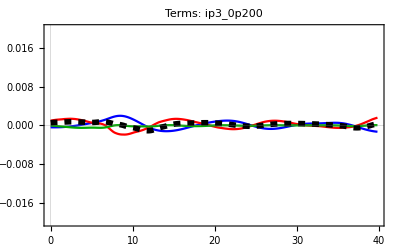
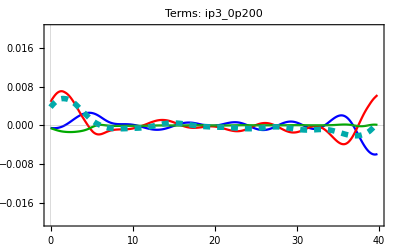
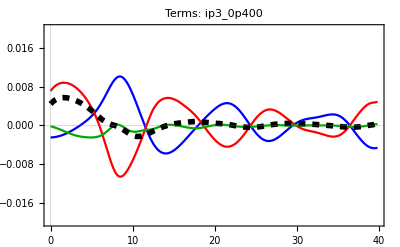
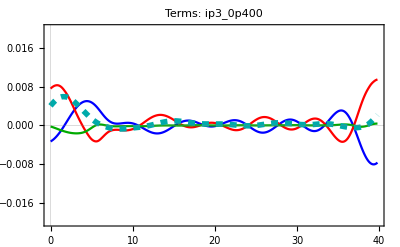
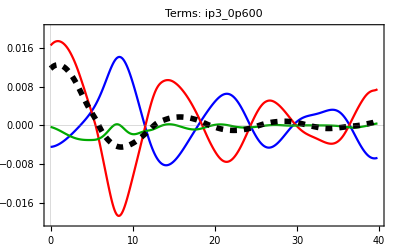
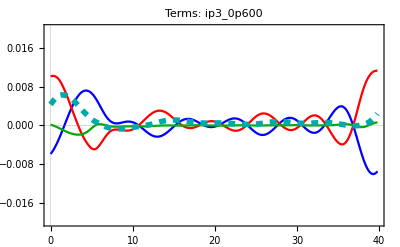
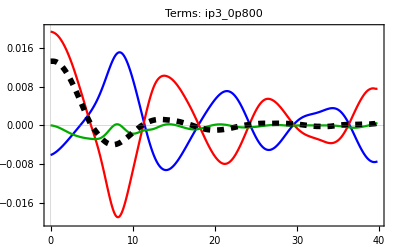
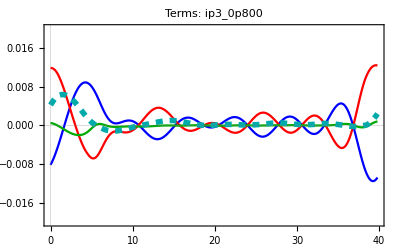
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
fcolors={{"fmuh1",Blue},{"fb1",Red},{"fw11",Darker[Green]}};
colorb1=Directive[Dashed,Black,Thickness[0.01]];
colorb2=Directive[Dashed,Darker[Cyan],Thickness[0.01]];

labels=<|
"fmuh1"->"(... x F_μ_h) term",
"fb1"->"(... x F_b_Ca) term",
"fw11"->"(... x F_W_(Ca, Ca)) term",
"fvarh11"->"(... x F_Σ_h) term"
|>;
leg=LineLegend[Join[fcolors[[;;,2]],{colorb1,colorb2}],Join[Table[labels[f[[1]]],{f,fcolors}],{"d<n_Ca>/dt = sum\nof all terms (rxns)","d<n_Ca>/dt = sum\nof all terms (params)"}]];

p=Grid[Table[{
pltMany[terms[ip3]["rxns_shallow"],fcolors,colorb1,False,"Terms: "<>ip3],
pltMany[terms[ip3]["params_shallow"],fcolors,colorb2,False,"Terms: "<>ip3],
leg
},{ip3,Keys[terms]}]]
```